## 1. Метод опорных векторов

### 1.1 Исходное фазовое пространство

```mathematica
Dimensions[Train=Import["C:\\NG\\NG21P05Problem.xlsx",{"Sheets","БельскаяЕ"}]⟦2;;4871⟧]
```

{4870,3}

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{2396},{2474}}

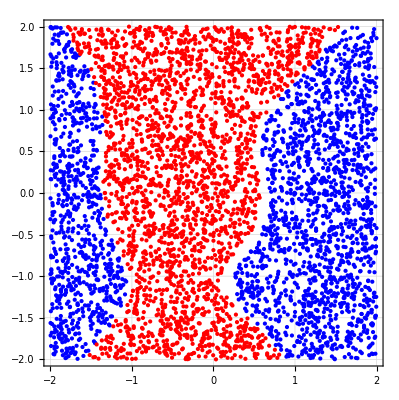

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

### 1.2 Расширенное фазовое пространство

Отображение из R^2 в R^14

```mathematica
func=With[{$=Flatten@Table[#1^(d-k)#2^k,{d,4},{k,0,d}]},$&];
```

```mathematica
XX=func@@@X
```

{{1.76391,-1.01903,3.11136,-1.79748,1.03843,5.48815,-3.17059,1.83169,-1.0582,9.68059,-5.59262,3.23094,-1.86656,1.07834},4869}
 |  |  |  |

### 1.4 Разделительная полоса

```mathematica
ClearAll[W]
```

```mathematica
W
```

{0.658564,-0.251599,0.0162556,-0.178073,-0.172511,0.0635462,-0.388711,-0.0915552,-0.0893327,0.162906,-0.381963,-0.297465,0.0348933,0.0199755,0.359126}

```mathematica
ClearAll[SVM];
SVM[w_]:=w.Prepend[#,-1]&
```

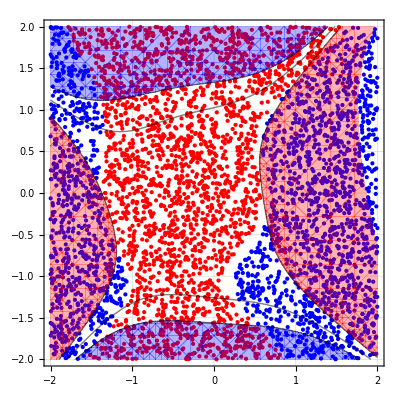

```mathematica
Show[Fig0, ContourPlot[SVM[W]@(func@@{x,y}),{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourShading->{Hue[0.00,1,1,0.3],GrayLevel[0.,0.],GrayLevel[0.,0.], Hue[0.67,1,1,0.3]}, GridLines->Automatic]]
```

У меня опорные точки в примере после n - го шага выбираются одни и те же. Я не очень понимаю, что не так. Поэтому весы не правильные, и картинка выглядит так.

## 2. Логический оператор AND как пример линейно разделимых классов

### 2.1 Фазовое пространство

Исходные данные

```mathematica
X={{1,-1},{-1,-1},{-1,1},{1,1}};
Y={-1,-1,-1,1};
```

```mathematica
iCold={1,2,3};
```

```mathematica
iWarm={4};
```

```mathematica
w1=RandomReal[{-2,2},3]
```

{-1.80225,-1.06233,0.415136}

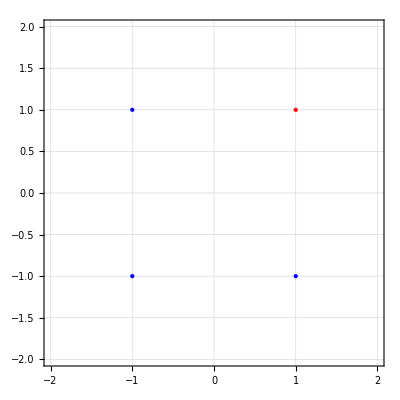

```mathematica
Fig0=Graphics[{PointSize[Large],Red, Point@X⟦iWarm⟧,Blue, Point@X⟦#⟧&/@iCold},Frame->True,GridLines->Automatic, PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
CreatePalette@Dynamic@Show[Fig0, ContourPlot[SVM[w1]@{x,y},{x,-5,5},{y,-5,5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.00,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0.67,1,1,0.3]},GridLines->Automatic]]
```

jyrvq_shm112FrontEndObject[LinkObject["jyrvq_shm", 3, 1]]112Untitled-13

## 3. Задача условной оптимизации

```mathematica
MapThread[#2({w11,w12}.#1-w10)≥1&,{X,Y}]
```

{w10-w11+w12≥1,w10+w11+w12≥1,w10+w11-w12≥1,-w10+w11+w12≥1}

Вычисление правильного положения разделительной полосы исходя из задачи условной оптимизации

```mathematica
W=Values@Last@FindMinimum[{#.#&@{w11,w12},And@@(MapThread[#2({w11,w12}.#1-w10)≥1&,{X,Y}])},{w10,w11,w12}]
```

{1.,1.,1.}

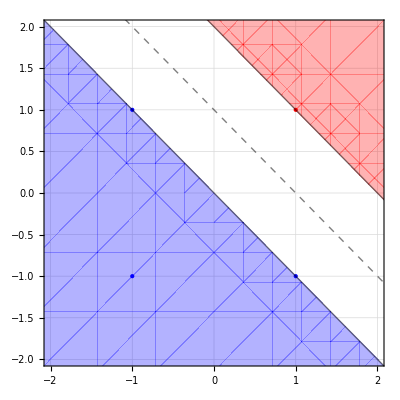

```mathematica
Show[Fig0, ContourPlot[SVM[W]@{x,y},{x,-5,5},{y,-5,5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0.00,1,1,0.3]},GridLines->Automatic]]
```

## 4. Логический оператор XOR и повышение размерности фазового пространства

Исходные данные

```mathematica
X={{-1,-1},{-1,1},{1,1},{1,-1}};
Y={-1,1,-1,1};
```

```mathematica
W=RandomReal[{-2,2},4]
```

{-1.3131,1.24993,0.50592,1.3129}

```mathematica
iWarm={2,4};
iCold={1,3};
```

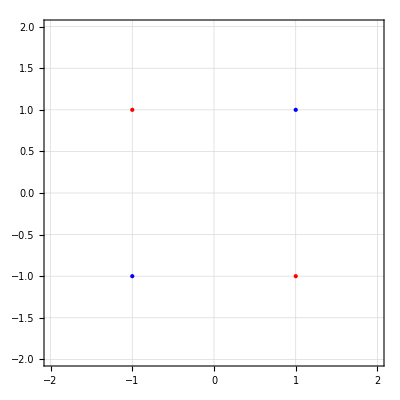

```mathematica
Fig0=Graphics[{PointSize[Large],Red, Point@X⟦iWarm⟧,Blue, Point@X⟦#⟧&/@iCold},Frame->True,GridLines->Automatic, PlotRange->{{-2,2},{-2,2}}]
```

Отображение из R^2 в R^3

```mathematica
f={#⟦1⟧,#⟦2⟧,(#⟦1⟧+#⟦2⟧)^2/4}&
```

```mathematica
XX=(f@X⟦#⟧)&/@Range[4]
```

{{-1,-1,1},{-1,1,0},{1,1,1},{1,-1,0}}

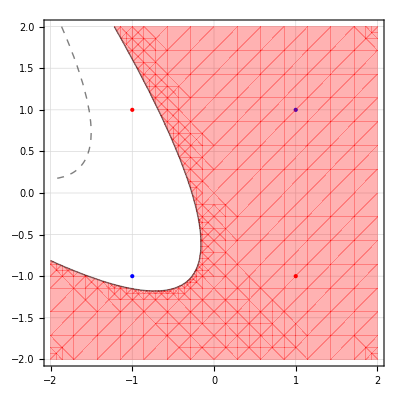

```mathematica
Show[Fig0, ContourPlot[SVM[W]@(f@{x,y}),{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0.00,1,1,0.3]},GridLines->Automatic]]
```

Аналогично предыдущему пункту

```mathematica
W=Values@Last@FindMinimum[{#.#&@{w11,w12,w13},And@@(MapThread[#2({w11,w12,w13}.#1-w10)≥1&,{XX,Y}])},{w10,w11,w12,w13}]
```

{-1.,-2.18924×10^-33,2.18919×10^-33,-2.}

```mathematica
Show[Graphics3D[{PointSize[Large],Red, Point@XX⟦iWarm⟧,Blue, Point@XX⟦iCold⟧},Axes->True,PlotRange->{{-2,2},{-2,2},{-2,2}}],ContourPlot3D[W⟦2;;4⟧.{x,y,z}-W⟦1⟧,{x,-2,2},{y,-2,2},{z,-2,2},Contours->{-1,0,1},ContourStyle->Map[Opacity[.2,#]&,{Blue,Gray,Red}]]]
```

-Graphics3D-

## 5. Опорные точки

```mathematica
Dimensions[Train=Import["C:\\NG\\NG21P05Problem.xlsx",{"Sheets","Train"}]⟦2;;⟧]
```

{180,3}

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{133},{47}}

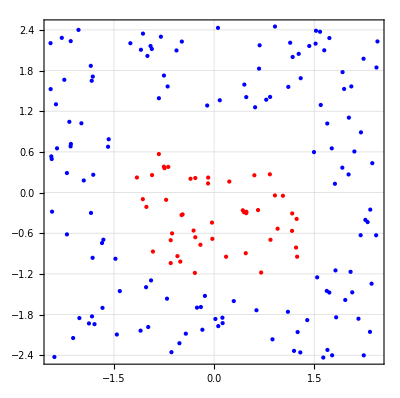

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

Аналогично пунктам выше перенос оьучающего набора в пятимерное пространство

```mathematica
ff=With[{$=Flatten@Table[#2^k#1^(d-k),{d,2},{k,0,d}]},$&];
```

```mathematica
XX=ff@@@X;
```

```mathematica
W=RandomReal[{-2,2},6]
```

{0.47324,0.453899,-1.58678,-0.261777,-1.92039,-1.87284}

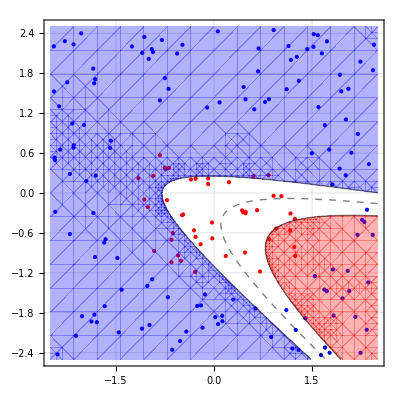

```mathematica
Show[Fig0, ContourPlot[SVM[W]@(ff@@{x,y}),{x,-2.5,2.5},{y,-2.5,2.5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0.00,1,1,0.3]},GridLines->Automatic]]
```

Опорные точки и точки - нарушители

```mathematica
iS=RandomSample[Join[iCold,iWarm],4]
iC=RandomSample[Join[iCold,iWarm],4]
```

{144,138,20,156}

{48,81,29,62}

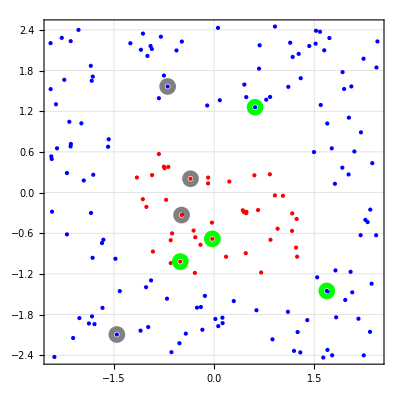

```mathematica
Show[Fig0, Graphics[{PointSize@Large,Green,AbsoluteThickness[4], Circle[#,Offset[4]]&/@X⟦iS⟧,Gray, Circle[#,Offset[4]]&/@X⟦iC⟧}]]
```

## 6. Множители Лагранжа и формулировка двойственной задачи

```mathematica
len=Length@X
```

180

Вектор из λ_n

```mathematica
ClearAll[λ]
```

```mathematica
λ=Table[Symbol["$λ"<>ToString@i],{i,len}];
```

Нахождение множителей Лагранжа (тут работает в качестве примера, используется ниже)

```mathematica
val=Values@Last@FindMinimum[{Sum[.5*λ⟦i⟧*λ⟦j⟧*Y⟦i⟧*Y⟦j⟧*(X⟦i⟧.X⟦j⟧),{i,1,len},{j,1,len}]-Total[λ],And@@(Join[λ⟦#⟧≥0&/@Range[len],{Sum[λ⟦i⟧*Y⟦i⟧,{i,1,len}]==0}])},λ]
```

```mathematica
Q=Table[Y⟦i⟧*Y⟦j⟧*(X⟦i⟧.X⟦j⟧),{i,iS},{j,iS}]
```

{{1.59749,-2.20087,0.831971,3.30567},{-2.20087,4.51484,-1.49206,-5.21819},{0.831971,-1.49206,0.51396,1.87646},{3.30567,-5.21819,1.87646,7.13772}}

```mathematica
Sum[λ⟦i⟧*Y⟦i⟧,{i,iS}]
```

-1. $λ159-1. $λ171+1. $λ58+1. $λ85

```mathematica
Values@Last@FindMinimum[{.5*Q.λ⟦iS⟧.λ⟦iS⟧-Total[λ⟦iS⟧],Sum[λ⟦i⟧*Y⟦i⟧,{i,iS}]==0},λ]
```

## 7. Последовательный метод активных ограничений

### 7.1 Инициализация множества опорных точек

Выполнение алгоритма обучения методом активных ограничений по шанам

```mathematica
iSC=First@RandomChoice[iCold,1]
```

121

```mathematica
i=1;
```

```mathematica
l={iSC,iSW};
```

```mathematica
iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iSC⟧];
```

```mathematica
While[True,If[i==1,iSC=First@Nearest[X⟦iCold⟧->"Index",X⟦iWarm⟧⟦iSW⟧];i--,iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iCold⟧⟦iSC⟧];i++];l=Join[l,{iSC,iSW}];
If[l⟦-1⟧==l⟦-3⟧ && l⟦-2⟧==l⟦-4⟧,Break[],Continue[]]]
```

```mathematica
{iSC,iSW}=l⟦{-2,-1}⟧
```

{55,39}

```mathematica
{iSC,iSW}=Flatten[Position[X,#]&/@{X⟦iCold⟧⟦iSC⟧,X⟦iWarm⟧⟦iSW⟧}]
iS=%;
```

{73,146}

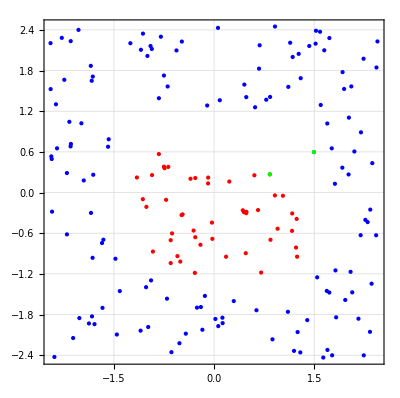

```mathematica
Show[Fig0,Graphics[{Green, PointSize@Large, Point@X⟦iS⟧}]]
```

### 7.2 Построение разделительной полосы

Нахождение весов и множителей Лагранжа

```mathematica
Q=Table[Y⟦i⟧*Y⟦j⟧*(XX⟦i⟧.XX⟦j⟧),{i,iS},{j,iS}]
```

{{8.53189,-3.19931},{-3.19931,1.31288}}

```mathematica
ClearAll[λ];λ=Table[Symbol["$λ"<>ToString@i],{i,len}];
```

```mathematica
λ⟦iS⟧=Values@Last@FindMinimum[{.5*Q.λ⟦iS⟧.λ⟦iS⟧-Total[λ⟦iS⟧],Sum[λ⟦i⟧*Y⟦i⟧,{i,iS}]==0},λ⟦iS⟧]
```

{0.580357,0.580357}

```mathematica
W=Sum[(λ⟦i⟧*Y⟦i⟧)XX⟦i⟧,{i,iS}]
```

{-0.383589,-0.190164,-0.89434,-0.387847,-0.16475}

```mathematica
w0=Median[(W.XX⟦#⟧-Y⟦#⟧)&/@iS]
```

-2.0948

```mathematica
WW=Prepend[W,w0]
```

{-2.0948,-0.383589,-0.190164,-0.89434,-0.387847,-0.16475}

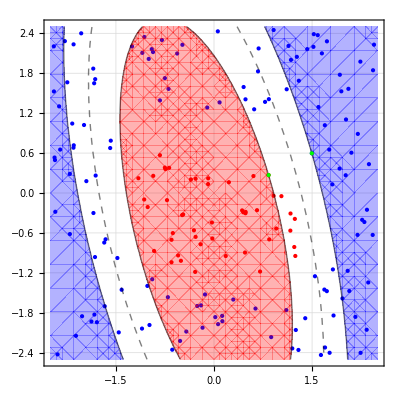

```mathematica
Show[Fig0, ContourPlot[SVM[WW]@(ff@@{x,y}),{x,-2.5,2.5},{y,-2.5,2.5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0], Hue[0.00,1,1,0.3]}, GridLines->Automatic], Graphics[{Green, PointSize@Large, Point@X⟦iS⟧}]]
```

### 7.3 Проверка опорных точек

### 7.4 Ложная опорная точка

```mathematica
iO=Delete[Range[len],{#}&/@iS];
```

Нахождение отступов и проверка условия

```mathematica
M={#,Y⟦#⟧(W.XX⟦#⟧-w0)}&/@iO;
M⟦First@First@Position[M,Min[M⟦All,2⟧]]⟧
First@M⟦First@First@Position[M,Min[M⟦All,2⟧]]⟧
```

{104,-1.96915}

104

```mathematica
iC={104};
iO=Delete[iO,104];
```

```mathematica
iS=Join[iS,iC]
```

{73,146,104}

```mathematica
iC={};
```

Аналогично пункту выше построение вектора W и нахождение множителей

```mathematica
Q=Table[Y⟦i⟧*Y⟦j⟧*(XX⟦i⟧.XX⟦j⟧),{i,iS},{j,iS}]
```

{{8.53189,-3.19931,0.171914},{-3.19931,1.31288,0.0445957},{0.171914,0.0445957,9.45587}}

```mathematica
ClearAll[λ];λ=Table[Symbol["$λ"<>ToString@i],{i,len}];
```

```mathematica
λ⟦iS⟧=Values@Last@FindMinimum[{.5*Q.λ⟦iS⟧.λ⟦iS⟧-Total[λ⟦iS⟧],Sum[λ⟦i⟧*Y⟦i⟧,{i,iS}]==0},λ⟦iS⟧]
```

{0.723536,1.01901,0.295475}

```mathematica
W=Sum[(λ⟦i⟧*Y⟦i⟧)XX⟦i⟧,{i,iS}]
```

{-0.318531,0.315641,-0.934514,-0.27757,-0.941578}

```mathematica
w0=Median[(W.XX⟦#⟧-Y⟦#⟧)&/@iS]
```

-1.9638

```mathematica
WW=Prepend[W,w0]
```

{-1.9638,-0.318531,0.315641,-0.934514,-0.27757,-0.941578}

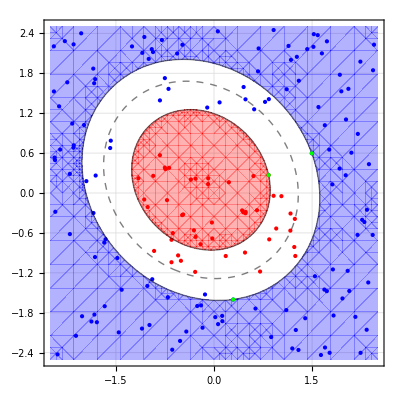

```mathematica
Show[Fig0, ContourPlot[SVM[WW]@(ff@@{x,y}),{x,-2.5,2.5},{y,-2.5,2.5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0], Hue[0.00,1,1,0.3]}, GridLines->Automatic], Graphics[{Green, PointSize@Large, Point@X⟦iS⟧}]]
```

Функция нахождения опорных точек

```mathematica
ClearAll[findP];findP[X_,iCold_, iWarm_]:=Module[{i=1,iSC, iSW,l},
iSC=First@RandomChoice[iCold,1];
iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iSC⟧];
l={iSC, iSW};
While[True,If[i==1,iSC=First@Nearest[X⟦iCold⟧->"Index",X⟦iWarm⟧⟦iSW⟧];i--,iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iCold⟧⟦iSC⟧];i++];l=Join[l,{iSC,iSW}];
If[l⟦-1⟧==l⟦-3⟧ && l⟦-2⟧==l⟦-4⟧,Break[],Continue[]]];
Flatten[Position[X,#]&/@{X⟦iCold⟧⟦iSC⟧,X⟦iWarm⟧⟦iSW⟧}]]
```

Функция для нахождение множителей Лагранжа

```mathematica
ClearAll[lag];lag[λ_,iS_,Q_,Y_]:=Values@Last@FindMinimum[{.5*Q.λ⟦iS⟧.λ⟦iS⟧-Total[λ⟦iS⟧],Sum[λ⟦i⟧*Y⟦i⟧,{i,iS}]==0},λ⟦iS⟧]
```

Классификатор (объединение шагов, выполненных выше). На вход: исходное множество всех точек

```mathematica
ClearAll[SVMF];SVMF[S_,k_]:=Module[{X,XX,Y,iCold, iWarm,iSC,iSW, λ,iS,M,min, iO,Q,len=Length@S,W, w0,WW,p},
X=S⟦All,1;;2⟧;
If[k==1,XX=ff@@@X,XX=func@@@X];
Y=S⟦All,3⟧;
{iCold=First[#]&/@Position[S,-1.],
iWarm=First[#]&/@Position[S, 1.]};

iS=findP[X, iCold, iWarm];

While[True,
iO=Delete[Range[len],{#}&/@iS];
Q=Table[Y⟦i⟧*Y⟦j⟧*(XX⟦i⟧.XX⟦j⟧),{i,iS},{j,iS}];

λ=Table[Symbol["$λ"<>ToString@i],{i,len}];
λ⟦iS⟧=lag[λ,iS, Q,Y];
W=Sum[(λ⟦i⟧*Y⟦i⟧)XX⟦i⟧,{i,iS}];
w0=Median[(W.XX⟦#⟧-Y⟦#⟧)&/@iS];
WW=Prepend[W,w0];

If[Length@iS>2&&Position[λ⟦iS⟧,_?NonPositive]≠{},
p=First@Position[λ,First@Sort[λ]];iS=Delete[iS,First@Position[iS,First@p]];
Continue[]];


M={#,Y⟦#⟧(W.XX⟦#⟧-w0)}&/@iO;
min=M⟦First@First@Position[M,Min[M⟦All,2⟧]]⟧;
If[Last@min<1,iS=Join[iS,{First@min}],Break[]]];
{WW,iS}
]
```

```mathematica
{WW2,iS1}=SVMF[Train,1]
```

{{-4.11068,0.0773118,-0.882806,-1.5109,-0.609077,-2.70477},{99,77,134,90,64,67}}

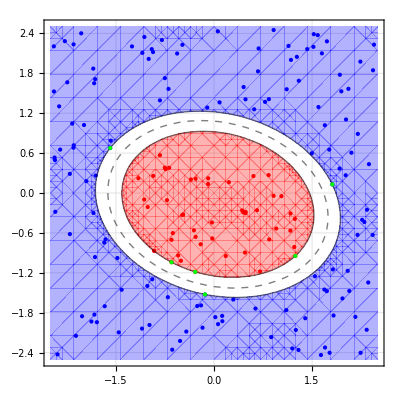

```mathematica
Show[Fig0, ContourPlot[SVM[WW2]@(ff@@{x,y}),{x,-2.5,2.5},{y,-2.5,2.5},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0], Hue[0.00,1,1,0.3]}, GridLines->Automatic], Graphics[{Green, PointSize@Large, Point@X⟦iS1⟧}]]
```

```mathematica
Dimensions[Train=Import["C:\\NG\\NG21P05Problem.xlsx",{"Sheets","БельскаяЕ"}]⟦2;;4871⟧]
```

{4870,3}

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{2396},{2474}}

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

```mathematica
{WW1,iS}=SVMF[Train,2]
```

{{-7.6018,-8.35776,0.817437,-0.640302,-3.02498,-6.7278,-3.39621,0.223846,-2.21689,5.29963,-7.55953,0.524145,-5.92323,1.88421,7.25958},{1379,1833,4537,2211,2371,3759,2663,1086,1045,744,801,921,1278,2919}}

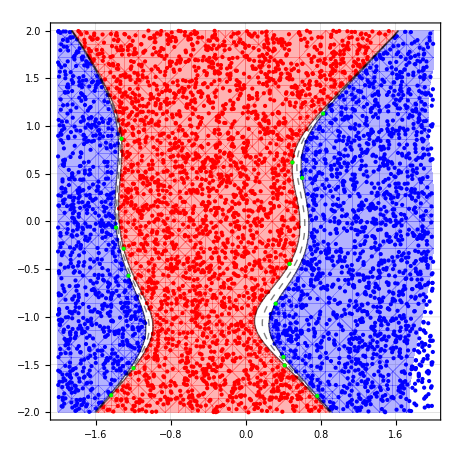

```mathematica
Show[Fig0, ContourPlot[SVM[WW1]@(func@@{x,y}),{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Black,Dashed,Black},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0], Hue[0.00,1,1,0.3]}, GridLines->Automatic], Graphics[{Green, PointSize@Large, Point@X⟦iS⟧}]]
```